```mathematica
(*dataPath ="Documents/workspace/Projects/Mathematica/data/generated_glyphs.txt";*)
dataPath ="Documents/workspace/Projects/Mathematica/data/glyphs.txt";
glyphs = Import[dataPath,"Table"];
GlyphEncoding:=#[[1]]&;
GlyphBBox:=#[[2;;5]]&;
GlyphMEC:=#[[6;;8]]&;
GlyphRuns:=Partition[#[[9;;Length[#]]],3]&;
MakeHBox[x_,b_,Δy_]:={{x⟦1⟧b,Δy b-x⟦2⟧b},{x⟦1⟧b+b,Δy b -(x⟦2⟧b+x⟦3⟧b)}};
MakeVBox[x_,b_,Δy_]:={{x⟦1⟧b,Δy b - x⟦2⟧b},{x⟦1⟧b+x⟦3⟧b,Δy b-(x⟦2⟧b+b)}};
GlyphBBoxArea[gl_]:=Block[{box=GlyphBBox[gl]},(box⟦4⟧-box⟦2⟧)*(box⟦3⟧-box⟦1⟧)];
GlyphArea[gl_]:=Block[{gr=GlyphRuns[gl]},Total[gr]⟦3⟧];
(* Horisontal *)
(* Left-Top corner *)
HTopLeft[gr_,h_]:=Block[{orig=First[gr]⟦1;;2⟧},{orig⟦1⟧,h-orig⟦2⟧}];
HLeftTop[gr_,h_]:=Block[{orig=First[Select[gr,TrueQ[#⟦1⟧==0]&]]⟦1;;2⟧},{orig[[1]],h-orig⟦2⟧}];
VLeftTop[gr_,h_]:=Block[{orig=First[gr]⟦1;;2⟧},{orig⟦1⟧,h-orig⟦2⟧}];
VTopLeft[gr_,h_]:=Block[{orig=First[Select[gr,TrueQ[#⟦2⟧==0]&]]⟦1;;2⟧},{orig[[1]],h-orig⟦2⟧}];
(* Top-Right corner *)
HTopRight[gr_,h_]:=Block[{orig=Last[Select[gr,TrueQ[#⟦2⟧==0]&]]},{orig⟦1⟧+orig⟦3⟧,h-orig⟦2⟧}];
HRightTop[gr_,w_,h_]:=Block[{orig=First[Select[gr,TrueQ[#⟦1⟧+#⟦3⟧==w]&]]},{w,h-orig⟦2⟧}];
VTopRight[gr_,h_]:=Block[{orig=Last[Select[gr,TrueQ[#⟦2⟧==0]&]]⟦1;;2⟧},{orig[[1]],h-orig⟦2⟧}];
VRightTop[gr_,w_,h_]:=Block[{orig=First[Select[gr,TrueQ[#⟦1⟧==w-1]&]]},{w,h-orig⟦2⟧}];
(* Bottom-Right *)
HRightBottom[gr_,w_,h_]:=Block[{orig=Last[Select[gr,TrueQ[#⟦1⟧+#⟦3⟧==w]&]]},{w,h-orig⟦2⟧}];
HBottomRight[gr_,h_]:=Block[{orig=Last[gr]},{orig⟦1⟧+orig⟦3⟧,h-orig⟦2⟧-1}];
VRightBottom[gr_,w_,h_]:=Block[{orig=Last[gr]},{w,h-orig⟦2⟧-orig⟦3⟧}];
VBottomRight[gr_,h_]:=Block[{orig=Last[Select[gr,TrueQ[#⟦2⟧+#⟦3⟧==h]&]]},{orig⟦1⟧,h-orig⟦2⟧-orig⟦3⟧}];
(* Bottom-Left *)
HBottomLeft[gr_,h_]:=Block[{orig=First[Select[gr,TrueQ[#⟦2⟧==h-1]&]]},{orig⟦1⟧,h-orig⟦2⟧-1}];
HLeftBottom[gr_,h_]:=Block[{orig=Last[Select[gr,TrueQ[#⟦1⟧==0]&]]},{orig⟦1⟧,h-orig⟦2⟧}];
VBottomLeft[gr_,h_]:=Block[{orig=First[Select[gr,TrueQ[#⟦2⟧+#⟦3⟧==h]&]]},{orig⟦1⟧,h-orig⟦2⟧-orig⟦3⟧}];
VLeftBottom[gr_,h_]:=Block[{orig=Last[Select[gr,TrueQ[#⟦1⟧==0]&]]},{orig⟦1⟧,h-orig⟦2⟧-orig⟦3⟧}];
(* Corner Polygons *)
CornerPolyCoordsLeftTop[gl_,h_]:=Block[{gr=GlyphRuns[gl],enc=GlyphEncoding[gl]},
If[enc!=0,
{{0,h},VTopLeft[gr,h],VLeftTop[gr,h],{0,h}},
{{0,h},HTopLeft[gr,h],HLeftTop[gr,h],{0,h}}
]
];
CornerPolyCoordsRightTop[gl_,w_,h_]:=Block[{gr=GlyphRuns[gl],enc=GlyphEncoding[gl]},
If[enc!=0,
{{w,h},VTopRight[gr,h],VRightTop[gr,w,h],{w,h}},
{{w,h},HTopRight[gr,h],HRightTop[gr,w,h],{w,h}}
]
];
CornerPolyCoordsRightBottom[gl_,w_,h_]:=Block[{gr=GlyphRuns[gl],enc=GlyphEncoding[gl]},
If[enc!=0,
{VRightBottom[gr,w,h],{w,0},{w,0},VBottomRight[gr,h]},
{HRightBottom[gr,w,h],{w,0},{w,0},HBottomRight[gr,h]}
]
];
CornerPolyCoordsLeftBottom[gl_,h_]:=Block[{gr=GlyphRuns[gl],enc=GlyphEncoding[gl]},
If[enc!=0,
{VBottomLeft[gr,h],{0,0},{0,0},VLeftBottom[gr,h]},
{HBottomLeft[gr,h],{0,0},{0,0},HLeftBottom[gr,h]}
]
];
(* Corner-cut points *)
SupportPoints[gl_,w_,h_]:=Block[{gr=GlyphRuns[gl],enc=GlyphEncoding[gl]},
If[enc!=0,
{VTopLeft[gr,h],VLeftTop[gr,h],VTopRight[gr,h],VRightTop[gr,w,h],VRightBottom[gr,w,h],VBottomRight[gr,h],VBottomLeft[gr,h],VLeftBottom[gr,h]},
{HTopLeft[gr,h],HLeftTop[gr,h],HTopRight[gr,h],HRightTop[gr,w,h],HRightBottom[gr,w,h],HBottomRight[gr,h],HBottomLeft[gr,h],HLeftBottom[gr,h]}
]
];
DrawBoxSrc[x_,b_]:=Block[{enc=GlyphEncoding[x],bbox=GlyphBBox[x],runs=GlyphRuns[x]},
If[enc==0,MakeVBox[#,b,bbox⟦4⟧-bbox⟦2⟧]&/@runs,MakeHBox[#,b,bbox⟦4⟧-bbox⟦2⟧]&/@runs]
];
DrawGlyphWithBBox[x_, b_]:=Block[{bbox=GlyphBBox[x]},
h=b(bbox⟦4⟧-bbox⟦2⟧);
w=b(bbox⟦3⟧-bbox⟦1⟧);
Graphics[
{
{EdgeForm[Thin],Gray,Opacity[.3],Line[Table[{{0,i},{w,i}},{i,1,h-1}]]},(* horisontal grid lines *)
{EdgeForm[Thin],Gray,Opacity[.3],Line[Table[{{i,h},{i,0}},{i,1,w-1}]]},(* vertical grid lines *)
{EdgeForm[Thin],LightBlue,Rectangle[#⟦1⟧,#⟦2⟧]}&/@DrawBoxSrc[x,b],
{EdgeForm[Thin],Opacity[.03],Rectangle[{0,0},{b(bbox⟦3⟧-bbox⟦1⟧),bbox⟦4⟧-bbox⟦2⟧}]}
}
]
];
DrawGlyphWithCenteredCircle[x_, b_]:=Block[{mec=GlyphMEC[x],bbox=GlyphBBox[x]},
h=b(bbox⟦4⟧-bbox⟦2⟧);
Graphics[
{
{EdgeForm[Thin],LightBlue,Rectangle[#⟦1⟧,#⟦2⟧]}&/@DrawBoxSrc[x,b],
Point[{mec⟦1⟧b,h-mec⟦2⟧b}],
Circle[{mec⟦1⟧b,h-mec⟦2⟧b},mec[[3]]b]
}
]
];
DrawGlyphWithBBoxAndCircle[x_, b_]:=Block[{mec=GlyphMEC[x],bbox=GlyphBBox[x]},
h=b(bbox⟦4⟧-bbox⟦2⟧);
Graphics[
{
{EdgeForm[Thin],LightBlue,Rectangle[#⟦1⟧,#⟦2⟧]}&/@DrawBoxSrc[x,b],
{EdgeForm[Thin],Opacity[.03],Rectangle[{0,0},{b(bbox⟦3⟧-bbox⟦1⟧),h}]},
Circle[{mec⟦1⟧b,h-mec⟦2⟧b},mec[[3]]b],
Point[{mec⟦1⟧b,h-mec⟦2⟧b}](* Circle center*)
}
]
];
DrawGlyphWithCenteredDisk[x_, b_]:=Block[{mec=GlyphMEC[x],bbox=GlyphBBox[x]},
h=b(bbox⟦4⟧-bbox⟦2⟧);
Graphics[
{
{EdgeForm[Thin],LightBlue,Rectangle[#⟦1⟧,#⟦2⟧]}&/@DrawBoxSrc[x,b],(* Runs *)
Point[{mec⟦1⟧b,h-mec⟦2⟧b}], (* Circle center*)
{EdgeForm[Thin],Opacity[.03],Disk[{mec⟦1⟧b,h-mec⟦2⟧b},mec⟦3⟧b]} (* Disk *)
}
]
];
DrawGlyphWithSectors[x_, b_]:=Block[{mec=GlyphMEC[x],bbox=GlyphBBox[x],sectors=Table[{i,i+Pi/8},{i,Pi/8,2Pi,Pi/8}]},
h=b(bbox⟦4⟧-bbox⟦2⟧);
Graphics[
{
{EdgeForm[Thin],LightBlue,Rectangle[#⟦1⟧,#⟦2⟧]}&/@DrawBoxSrc[x,b],(* Runs *)
{EdgeForm[{Thin,Gray}],Opacity[.03],Disk[{mec⟦1⟧b,h-mec⟦2⟧b},mec⟦3⟧b,#]}&/@sectors,
Point[{mec⟦1⟧b,h-mec⟦2⟧b}] (* Circle center*)
}
]
];
DrawGlyphWithCircleSupport[x_, b_]:=Block[{mec=GlyphMEC[x],bbox=GlyphBBox[x]},
h=b(bbox⟦4⟧-bbox⟦2⟧);
w=b(bbox⟦3⟧-bbox⟦1⟧);
Graphics[
{
{EdgeForm[Thin],LightBlue,Rectangle[#⟦1⟧,#⟦2⟧]}&/@DrawBoxSrc[x,b],
{EdgeForm[Thin],Opacity[.03],Rectangle[{0,0},{b(bbox⟦3⟧-bbox⟦1⟧),h}]},
Circle[{mec⟦1⟧b,h-mec⟦2⟧b},mec[[3]]b],
Point[{mec⟦1⟧b,h-mec⟦2⟧b}],(* Circle center*)
{EdgeForm[Red],Opacity[.05],Polygon[CornerPolyCoordsLeftTop[x,h]]},
{EdgeForm[Red],Opacity[.05],Polygon[CornerPolyCoordsRightTop[x,w,h]]},
{EdgeForm[Red],Opacity[.05],Polygon[CornerPolyCoordsRightBottom[x,w,h]]},
{EdgeForm[Red],Opacity[.05],Polygon[CornerPolyCoordsLeftBottom[x,h]]},
{AbsolutePointSize[3],Green,Opacity[.8],Point[SupportPoints[x,w,h]]}
}
]
];
SectorIndex[x_,y_,NumFeatures_]:=Block[
{absx=Abs[x],absy=Abs[y],ω=.5 NumFeatures/π,ϵ=.00000001,half=.5NumFeatures,
quat=.25NumFeatures,tquat=.75 NumFeatures,index},
index=Which[
absx<ϵ&&absy<ϵ,0,
absy<ϵ&&x<0.,half,
absx<ϵ&&y>0.,quat,
absx<ϵ&&y<0.,tquat,
x>0.&&y>0.,ω ArcTan[x,y],
x<0.&&y>0.,ω ArcTan[-x,y]+quat,
x<0.&&y<0.,ω ArcTan[-x,-y]+half,
x>0.&&y<0.,ω ArcTan[x,-y]+tquat,
True, 0.
];
(* Emulate jumps over NumFeatures by Mod *)
Mod[IntegerPart[index+.5],NumFeatures]
];
SectorFeatures[gl_,NumFeatures_]:=Block[
{gr=GlyphRuns[gl],enc=GlyphEncoding[gl],
mec=GlyphMEC[gl],data,res},
(* The amount of data items is the same as runs. 
 For each run therere are a table of pairs: { offset, result } 
 *)
data=If[enc!=0,
Table[{SectorIndex[#⟦1⟧-mec⟦1⟧,#⟦2⟧-mec⟦2⟧+i,NumFeatures],
Sqrt[(#⟦1⟧-mec⟦1⟧)^2+(#⟦2⟧-mec⟦2⟧+i)^2]},{i,0,#⟦3⟧}]&/@gr,
Table[{SectorIndex[#⟦1⟧-mec⟦1⟧+i,#⟦2⟧-mec⟦2⟧,NumFeatures],
Sqrt[(#⟦1⟧-mec⟦1⟧+i)^2+(#⟦2⟧-mec⟦2⟧)^2]},{i,0,#⟦3⟧}]&/@gr
];
(* res item format : { counts, hypots } *)
res=Table[{0.,0.},{NumFeatures}];
Scan[res⟦#⟦1⟧+1⟧+={1.,#⟦2⟧}&,data,{2}];(* collect results only at level 2 *)
Table[If[res⟦i,1⟧≠0,res⟦i,2⟧/(mec⟦3⟧res⟦i,1⟧),0],{i,1,NumFeatures}]
];
CircleFeatures[gl_]:=Block[
{gr=GlyphRuns[gl],enc=GlyphEncoding[gl],
mec=GlyphMEC[gl],data,res},
(* The amount of data items is the same as runs. 
 For each run therere are a table of pairs: { offset, result } 
 *)
data=Flatten[
If[enc!=0,
Table[ {ArcTan[#⟦1⟧-mec⟦1⟧,#⟦2⟧-mec⟦2⟧+i],Sqrt[(#⟦1⟧-mec⟦1⟧)^2+(#⟦2⟧-mec⟦2⟧+i)^2]/mec⟦3⟧},{i,0,#⟦3⟧}]&/@gr,
Table[{ArcTan[#⟦1⟧-mec⟦1⟧+i,#⟦2⟧-mec⟦2⟧],Sqrt[(#⟦1⟧-mec⟦1⟧+i)^2+(#⟦2⟧-mec⟦2⟧)^2]/mec⟦3⟧},{i,0,#⟦3⟧}]&/@gr
]
,1];
SmoothHistogram3D[data]
];
```

```mathematica
symbolsForDisser={glyphs⟦2⟧,glyphs⟦1⟧,glyphs⟦66⟧,glyphs⟦71⟧,glyphs⟦43⟧};
```

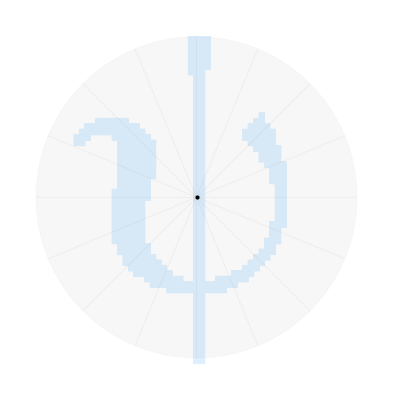
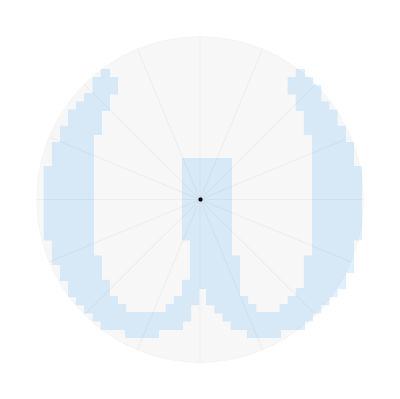
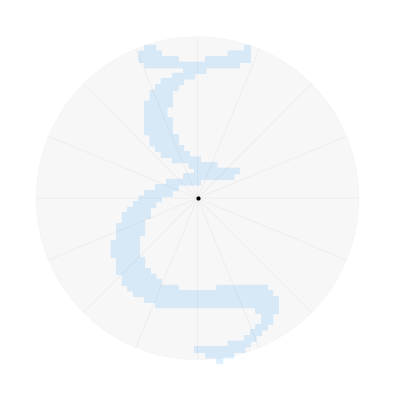
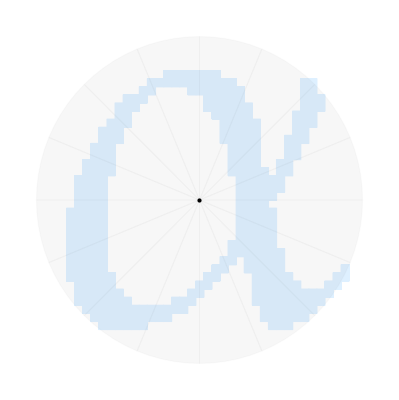
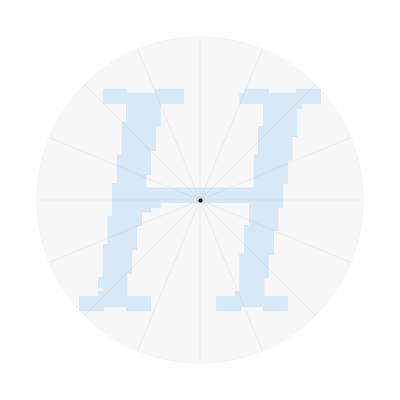

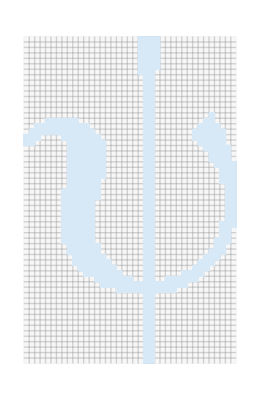
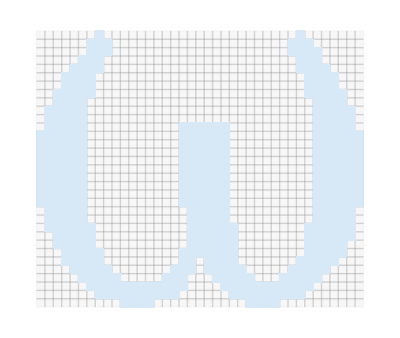
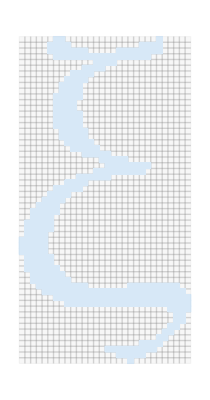

0.611087 | 0.797355 | 0.644536 | 0.547329 | 0.335782
0.526106 | 0.821613 | 0 | 0.550298 | 0.386688
0.514346 | 0.795281 | 0.750747 | 0.687114 | 0.540014
0.538273 | 0.620527 | 0.766286 | 0.658033 | 0.648339
0.524363 | 0.69126 | 0.641827 | 0.655236 | 0.418455
0.485681 | 0.847566 | 0.47201 | 0.788496 | 0.524473
0.523145 | 0.837918 | 0.585076 | 0.875142 | 0.763582
0.541747 | 0.701642 | 0.61834 | 0.775794 | 0.742781
0.518586 | 0.596807 | 0.502639 | 0.654872 | 0.374637
0.549841 | 0.837315 | 0.212836 | 0.682767 | 0.393689
0.576256 | 0.816975 | 0.372625 | 0.714163 | 0.611314
0.0694071 | 0.206554 | 0.609203 | 0.76122 | 0.628142
0.611216 | 0.640392 | 0.650816 | 0.618276 | 0.348438
0.516572 | 0.802232 | 0 | 0.486788 | 0.410955
0.52892 | 0.776068 | 0.254965 | 0.652872 | 0.682079
0.0694071 | 0.2027 | 0.677249 | 0.548478 | 0.641266

{{2340,463,50,0.107991},{1287,461,46,0.0997831},{1710,358,61,0.170391},{1120,372,58,0.155914},{2397,776,87,0.112113}}

```mathematica
DrawGlyphWithSectors[#, 1]&/@symbolsForDisser
DrawGlyphWithCenteredDisk[#, 1]&/@symbolsForDisser;
DrawGlyphWithBBox[#, 1]&/@symbolsForDisser
DrawGlyphWithBBoxAndCircle[#, 1]&/@symbolsForDisser;
DrawGlyphWithCircleSupport[#,1]&/@symbolsForDisser
SectorFeatures[#,16]&/@symbolsForDisser//Transpose//Grid[#,Frame->All]&
{GlyphBBoxArea[#],GlyphArea[#],Length[GlyphRuns[#]],N[Length[GlyphRuns[#]]/GlyphArea[#]]}&/@symbolsForDisser
```

```mathematica
CircleFeatures[#]&/@{glyphs⟦6⟧,glyphs⟦7⟧,glyphs⟦66⟧,glyphs⟦67⟧}
(* :TODO: do the subdivision process on a set of radial data { ρ, ω }, as done in KD-tree, and record each cut position as feature *)
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

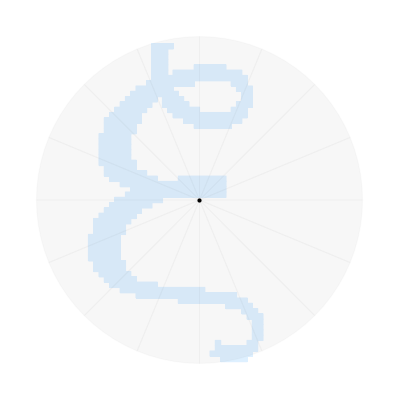
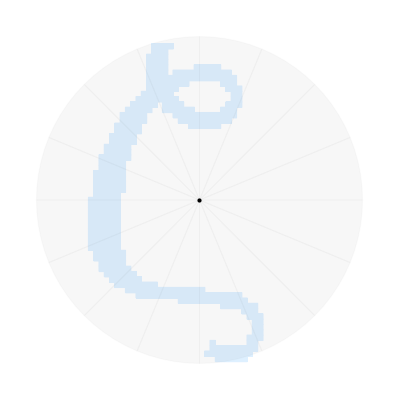
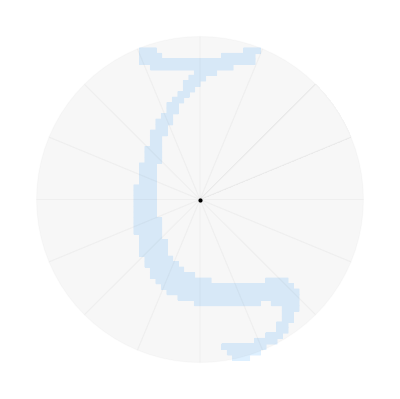
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawGlyphWithSectors[#, 1]&/@{glyphs⟦6⟧,glyphs⟦7⟧,glyphs⟦66⟧,glyphs⟦67⟧}
```